```mathematica
SetDirectory[NotebookDirectory[]];
```

Lattice (HotQCD)

```mathematica
TcFun[muB_,Tc0_,kappa2_,kappa4_]=Tc0(1-kappa2(muB/Tc0)^2-kappa4(muB/Tc0)^4)
```

(1-(kappa4 muB^4)/Tc0^4-(kappa2 muB^2)/Tc0^2) Tc0

```mathematica
dTcFun[muB_,Tc0_,kappa2_,kappa4_,dTc0_,dkappa2_,dkappa4_]=(D[TcFun[muB,Tc0,kappa2,kappa4],Tc0]^2dTc0^2+D[TcFun[muB,Tc0,kappa2,kappa4],kappa2]^2dkappa2^2+D[TcFun[muB,Tc0,kappa2,kappa4],kappa4]^2 dkappa4^2)^(1/2)//Simplify
```

√((dkappa4^2 muB^8 Tc0^2+dkappa2^2 muB^4 Tc0^6+dTc0^2 (3 kappa4 muB^4+kappa2 muB^2 Tc0^2+Tc0^4)^2)/Tc0^8)

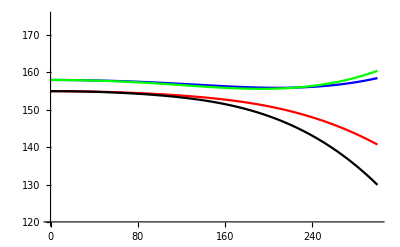

```mathematica
Show[Plot[TcFun[muB,156.5(*Tc0*),0.012(*kappa2*),0(*kappa4*)]-dTcFun[muB,156.5(*Tc0*),0.012(*kappa2*),0(*kappa4*),1.5(*dTc0*),0.004(*dkappa2*),0.004(*dkappa4*)],{muB,0,300},PlotRange->{Automatic, {120,175}} ,PlotStyle->Red],Plot[TcFun[muB,156.5(*Tc0*),0.012(*kappa2*),0(*kappa4*)]+dTcFun[muB,156.5(*Tc0*),0.012(*kappa2*),0(*kappa4*),1.5(*dTc0*),0.004(*dkappa2*),0.004(*dkappa4*)],{muB,0,300},PlotRange->{Automatic, {135,175}} ,PlotStyle->Blue],Plot[TcFun[muB,156.5(*Tc0*),0.016(*kappa2*),0.001(*kappa4*)]-dTcFun[muB,156.5(*Tc0*),0.016(*kappa2*),0.001(*kappa4*),1.5(*dTc0*),0.006(*dkappa2*),0.007(*dkappa4*)],{muB,0,300},PlotRange->{Automatic, {120,175}} ,PlotStyle->Black],Plot[TcFun[muB,156.5(*Tc0*),0.016(*kappa2*),0.001(*kappa4*)]+dTcFun[muB,156.5(*Tc0*),0.016(*kappa2*),0.001(*kappa4*),1.5(*dTc0*),0.006(*dkappa2*),0.007(*dkappa4*)],{muB,0,300},PlotRange->{Automatic, {120,175}} ,PlotStyle->Green]]
```

Phase line (Nf=2+1)

```mathematica
pb1=Import["./CEP/pb-Nf2p1.dat"];
```

```mathematica
pb=Drop[pb1,1];
```

```mathematica
Tcdata=Import["./CEP/Tc.dat"];
```

```mathematica
lendata=Length[pb];
```

```mathematica
muBtoTlow=Table[{pb[[i,1]],pb[[i,2]]},{i,lendata}];
```

```mathematica
muBtoThigh=Table[{pb[[i,1]],pb[[i,3]]},{i,lendata}];
```

```mathematica
muBtoTc=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,lendata}];
```

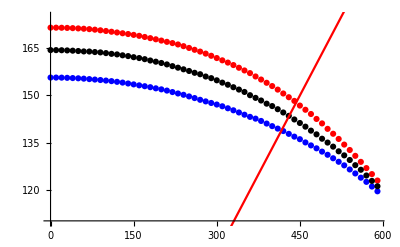

```mathematica
Show[ListPlot[muBtoThigh,PlotRange->{Automatic, {110,175}} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/3,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
muBtoTlow2=Table[{pb[[i,1]],pb[[i,2]]},{i,42}];
```

```mathematica
muBtoThigh2=Table[{pb[[i,1]],pb[[i,3]]},{i,45}];
```

```mathematica
muBtoTc2=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,44}];
```

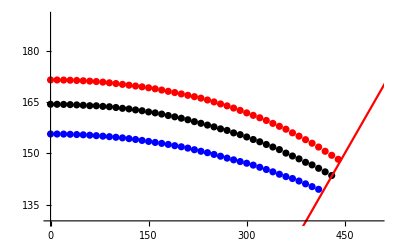

```mathematica
Show[ListPlot[muBtoThigh2,PlotRange->{{0,500}, {130,190}} ,PlotStyle->Red],ListPlot[muBtoTlow2,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc2,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/3,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
TlowPoly2[x_]=Fit[muBtoTlow2,  {1,x^2,x^4},x];
```

```mathematica
ThighPoly2[x_]=Fit[muBtoThigh2, {1,x^2,x^4},x];
```

```mathematica
TcPoly2[x_]=Fit[muBtoTc2, {1,x^2,x^4},x];
```

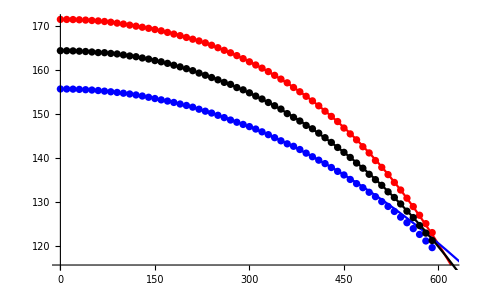

```mathematica
Show[Plot[ThighPoly2[muB],{muB,0,620},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],Plot[TlowPoly2[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPoly2[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black]]
```

```mathematica
FindRoot[ {TlowPoly2[x]== ThighPoly2[x]},{x,600}]
```

{x→600.981}

```mathematica
TlowPoly2[600.9806990097809]
```

115.461

```mathematica
TlowPoly[x_]=Fit[muBtoTlow,  {1,x^2,x^4},x];
```

```mathematica
ThighPoly[x_]=Fit[muBtoThigh, {1,x^2,x^4},x];
```

```mathematica
TcPoly[x_]=Fit[muBtoTc, {1,x^2,x^4},x];
```

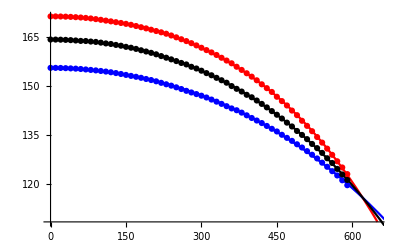

```mathematica
Show[Plot[ThighPoly[muB],{muB,0,650},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],Plot[TlowPoly[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPoly[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc,PlotRange->{Automatic, Automatic} ,PlotStyle->Black]]
```

```mathematica
FindRoot[ {TlowPoly[x]== ThighPoly[x]},{x,600}]
```

{x→620.225}

```mathematica
TlowPoly[620.2245188857656]
```

115.917

```mathematica
(*d2TlowdT2[muB_]=D[TlowPoly2[muB],{muB,2}];*)
```

```mathematica
(*d2TlowdT2[0]*TlowPoly2[0]/(-2)*)
```

0.013742

```mathematica
(*d2ThighdT2[muB_]=D[ThighPoly2[muB],{muB,2}];*)
```

```mathematica
(*d2ThighdT2[0]*ThighPoly2[0]/(-2)*)
```

0.0157323

```mathematica
(*d2TcdT2[muB_]=D[TcPoly2[muB],{muB,2}];*)
```

```mathematica
(*d2TcdT2[0]*TcPoly2[0]/(-2)*)
```

0.0161135

```mathematica
d2TlowdT2[muB_]=D[TlowPoly2[muB],{muB,2}];
```

```mathematica
d2TlowdT2[0]*TlowPoly2[0]/(-2)
```

0.014718

```mathematica
d2ThighdT2[muB_]=D[ThighPoly2[muB],{muB,2}];
```

```mathematica
d2ThighdT2[0]*ThighPoly2[0]/(-2)
```

0.0161362

```mathematica
d2TcdT2[muB_]=D[TcPoly2[muB],{muB,2}];
```

```mathematica
d2TcdT2[0]*TcPoly2[0]/(-2)
```

0.0166919

muB/T=2

```mathematica
muBtoTlow2=Table[{pb[[i,1]],pb[[i,2]]},{i,30}];
```

```mathematica
muBtoThigh2=Table[{pb[[i,1]],pb[[i,3]]},{i,33}];
```

```mathematica
muBtoTc2=Table[{pb[[i,1]],Tcdata[[i,1]]},{i,32}];
```

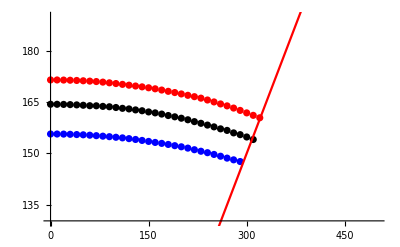

```mathematica
Show[ListPlot[muBtoThigh2,PlotRange->{{0,500}, {130,190}} ,PlotStyle->Red],ListPlot[muBtoTlow2,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc2,PlotRange->{Automatic, Automatic} ,PlotStyle->Black],Plot[muB/2,{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
TlowPoly2[x_]=Fit[muBtoTlow2,  {1,x^2,x^4},x];
```

```mathematica
ThighPoly2[x_]=Fit[muBtoThigh2, {1,x^2,x^4},x];
```

```mathematica
TcPoly2[x_]=Fit[muBtoTc2, {1,x^2,x^4},x];
```

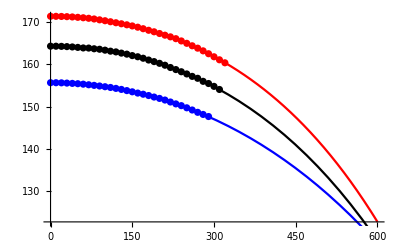

```mathematica
Show[Plot[ThighPoly2[muB],{muB,0,600},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],Plot[TlowPoly2[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],Plot[TcPoly2[muB],{muB,0,1000},PlotRange->{Automatic, Automatic} ,PlotStyle->Black],ListPlot[muBtoThigh2,PlotRange->{Automatic, Automatic} ,PlotStyle->Red],ListPlot[muBtoTlow2,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],ListPlot[muBtoTc2,PlotRange->{Automatic, Automatic} ,PlotStyle->Black]]
```

```mathematica
(*d2TlowdT2[muB_]=D[TlowPoly2[muB],{muB,2}];*)
```

```mathematica
(*d2TlowdT2[0]*TlowPoly2[0]/(-2)*)
```

0.0139289

```mathematica
(*d2ThighdT2[muB_]=D[ThighPoly2[muB],{muB,2}];*)
```

```mathematica
(*d2ThighdT2[0]*ThighPoly2[0]/(-2)*)
```

0.0157614

```mathematica
(*d2TcdT2[muB_]=D[TcPoly2[muB],{muB,2}];*)
```

```mathematica
(*d2TcdT2[0]*TcPoly2[0]/(-2)*)
```

0.0159445

```mathematica
d2TlowdT2[muB_]=D[TlowPoly2[muB],{muB,2}];
```

```mathematica
d2TlowdT2[0]*TlowPoly2[0]/(-2)
```

0.0144635

```mathematica
d2ThighdT2[muB_]=D[ThighPoly2[muB],{muB,2}];
```

```mathematica
d2ThighdT2[0]*ThighPoly2[0]/(-2)
```

0.0164707

```mathematica
d2TcdT2[muB_]=D[TcPoly2[muB],{muB,2}];
```

```mathematica
d2TcdT2[0]*TcPoly2[0]/(-2)
```

0.0164274